## 収束性のチェック

```mathematica
Clear["Global`*"]
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
(*json="/Users/tomoaki/BEM/Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)

jsonLINEAR="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json"
jsonQUAD="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"

(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_middle/result.json"*)
jsonInfo[json]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json

/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json

no. | title | length
1 | cpu_time | 422
2 | eq_of_motion | 422
3 | gauge1_intersection | 422
4 | gauge2_intersection | 422
5 | gauge3_intersection | 422
6 | gradPhi_worst_grad | 422
7 | gradPhi_worst_iteration | 422
8 | gradPhi_worst_value | 422
9 | simulation_time | 422
10 | wall_clock_time | 422
11 | water_E | 422
12 | water_EK | 422
13 | water_EP | 422
14 | water_face_size | 422
15 | water_point_size | 422
16 | water_volume | 422

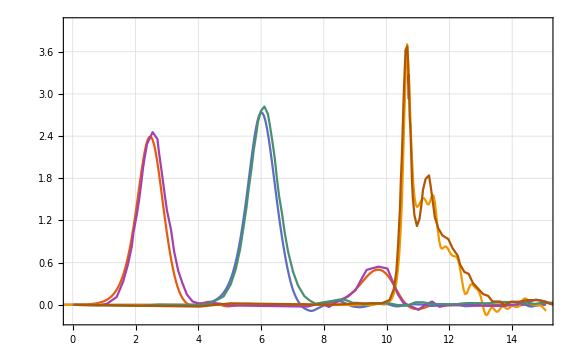

```mathematica
gauge1EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
gauge2EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
gauge3EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];

h=0.25;
shiftt=4.96;
ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge3_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge3_intersection",3]-h)*100}ᵀ,
gauge1EXP,
gauge2EXP,
gauge3EXP}
,GridLines->Automatic
,ImageSize->Large
,PlotRange->{{0,15},{-0.2,4}}
,Evaluate[plot2Doption]]
```